# Agent Network

## Create Base/Seed Network

```mathematica
network[nodes_,conn_]:=Flatten[Table[Table[i->Mod[i+j,nodes,1],{i,1,If[j≥Quotient[nodes+1,2],nodes/2,nodes],1}],{j,1,conn-1,1}]]
```

#### Degree Computation for base network

```mathematica
k = network[500,4];
```

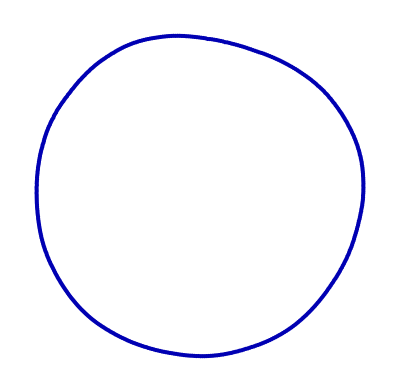

```mathematica
GraphPlot[k,DirectedEdges->False,VertexLabeling->False]
```

```mathematica
DistributionChart[k];
Histogram[k];
```

```mathematica
pr1 = PageRankVector[k];
ListPlot[pr1]
```

## Recalibrating connections

```mathematica
network2 = rewirednetwork[p_,network_]:=Table[If[RandomReal[]>p,network[[i]],network[[i]][[1]]->RandomChoice[Cases[network[[All,2]],Except[network[[i]][[1]]]]]],{i,Dimensions[network][[1]]}]
```

```mathematica
k2 = rewirednetwork[0.25,network[50,4]];
```

```mathematica
GraphPlot[k2,DirectedEdges->False,VertexLabeling->False];
```

```mathematica
DistributionChart[k2];
Histogram[k2];
```

```mathematica
Needs["GraphUtilities`"]
v = VertexList[k2];
e = EdgeList[k2];
```

PageRankVector::shdw: Symbol "PageRankVector" appears in multiple contexts {"GraphUtilities`", "Global`"}; definitions in context "GraphUtilities`" may shadow or be shadowed by other definitions.

```mathematica
pr = PageRankVector[k2];
```

```mathematica
npr = pr * 1000
max = Max[npr]
```

{9.45561,12.1347,15.0812,10.7112,6.03484,8.98288,12.5771,22.9867,9.5129,25.1936,12.0581,15.6247,29.8739,24.8186,13.5955,25.5381,13.7993,12.6879,19.4504,12.4207,18.7571,3.,20.2853,23.5294,15.4141,28.4245,29.651,30.5048,23.5063,18.0612,38.0281,25.5261,25.6261,25.0303,24.1299,29.4996,21.9174,29.2288,30.4143,17.9416,13.7974,26.5474,19.5145,19.9601,17.6137,21.2047,19.6539,20.7865,27.1237,22.7845}

38.0281

```mathematica
ListPlot[Sort[pr]];
```

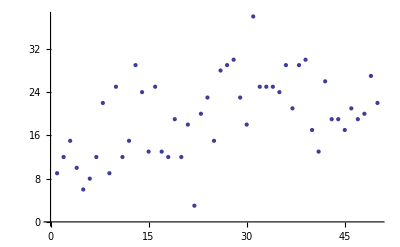

```mathematica
ListPlot[npr]
```

```mathematica
freqNpr = List[];
Do [AppendTo[freqNpr, Count[npr,np]],{np,max}]
Length[freqNpr]
freqNpr;
```

38

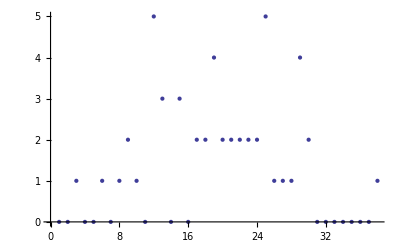

```mathematica
ListPlot[freqNpr]
```

```mathematica
ClosenessCentrality[k2];
```

```mathematica
numConnection = List[]
Do[ AppendTo[numConnection,Count[e,{t,x_}] + Count[e,{x_,t}]], {t,v} ]
numConnection;
```

{}

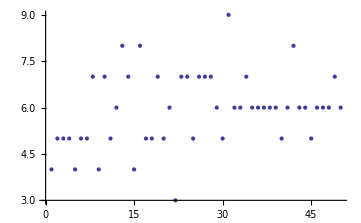

```mathematica
ListPlot[numConnection]
```

```mathematica
freqConnection = List[]
Do [AppendTo[freqConnection, Count[numConnection,con]],{con,v}]
freqConnection;
```

{}

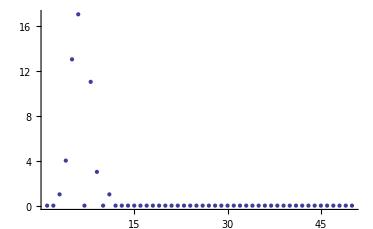

```mathematica
ListPlot[freqConnection]
```